```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
obj = QuestionObject["Which sample has a larger mean?", 
 AssessmentFunction[{"test" -> False, 755 -> True, 868 -> False}]]
```

```mathematica
obj[]
```

[]

```mathematica
QuestionInterface
```

```mathematica
AssessmentFunction[{"test" -> False, 755 -> True, 868 -> False}][868]
```

AssessmentResultObject[…]

```mathematica
Dynamic[obj]
```

```mathematica
AssessmentFunction[{"test" -> False, 755 -> True, 868 -> False}]
```

AssessmentFunction[…]

```mathematica
data = DeleteCases[Import["Projects/Wolfram/Mom/WeekendDataPrePost.csv"][[2;;]][[All, 1]], ""]
```

{8,27,12,20,15,26,13,27,6,12,18,13,11,16,8,20,15,15,12,16,8,20,11,24,16,16,13,26,12,21,8,22,12,20,15,18,17,24,13,23,15,17,14,26,12,27,13,18,13,18,11,17,19}

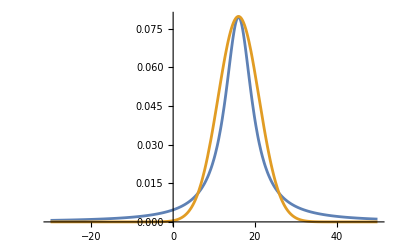

```mathematica
Plot[{PDF[CauchyDistribution[16, 4], x],PDF[NormalDistribution[16, 5], x]} , {x, -30, 50}, PlotRange->All]
```

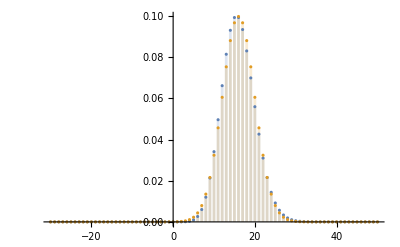

```mathematica
DiscretePlot[{PDF[PoissonDistribution[16],x],PDF[NormalDistribution[16, 4],x]}, {x, -30, 50}, PlotRange->All]
```

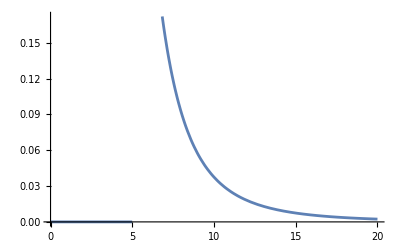

```mathematica
Plot[PDF[ParetoDistribution[5, 3], x], {x, 0, 20}]
```

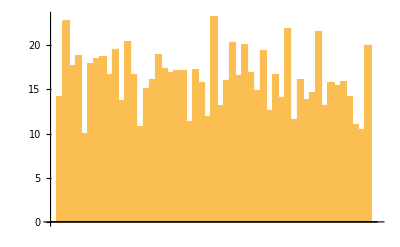

```mathematica
BarChart[RandomVariate[NormalDistribution[16, 3], 51]]
```

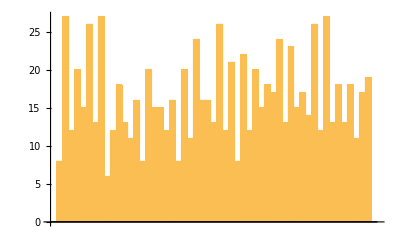
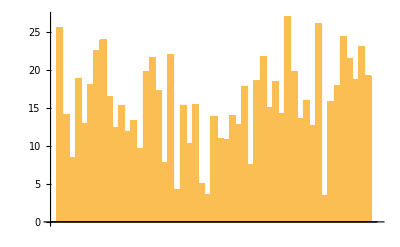

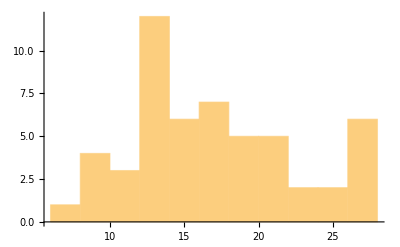
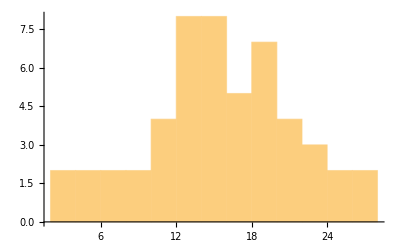

```mathematica
simData = RandomVariate[NormalDistribution[16, 5], 51];
{BarChart[data], BarChart[simData]}
{Histogram[data, n=10, PlotRange->12], Histogram[simData, n = 10, PlotRange->12] }
```

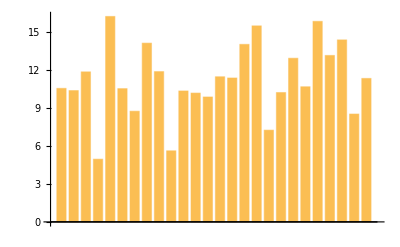
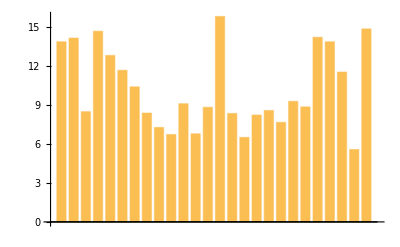
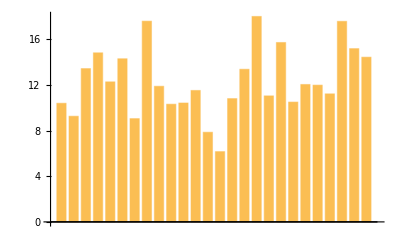
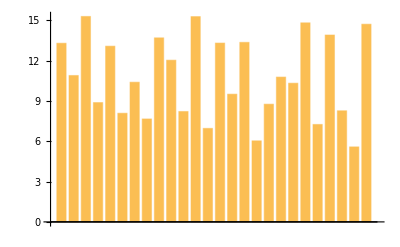
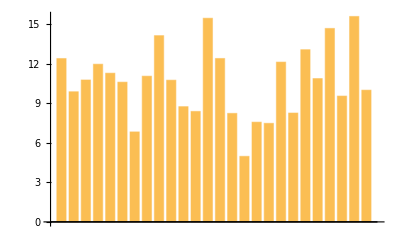
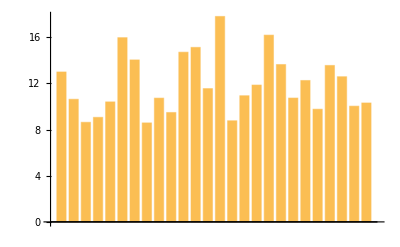
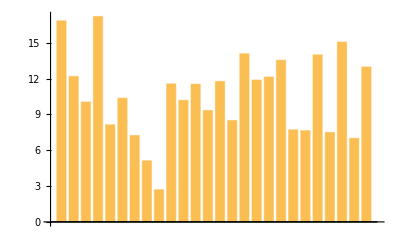
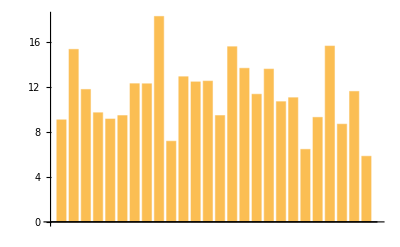
{{{-Graphics-,del},{-Graphics-,reg}},{{-Graphics-,del},{-Graphics-,reg}},{{-Graphics-,reg},{-Graphics-,del}},{{-Graphics-,reg},{-Graphics-,del}},{{-Graphics-,del},{-Graphics-,reg}},{{-Graphics-,reg},{-Graphics-,del}},{{-Graphics-,reg},{-Graphics-,del}},{{-Graphics-,del},{-Graphics-,reg}}}

```mathematica
n = 26;
mu = 10;
sig = 3;
delta = 2;
nCharts = 8;
regular = RandomVariate[NormalDistribution[mu, sig], {nCharts, n}];
withDelta = RandomVariate[NormalDistribution[mu+delta, sig], {nCharts, n}];
barCharts = MapThread[{{BarChart[#1, PlotRange->20], "reg"}, {BarChart[#2, PlotRange->20], "del"}}&, {regular, withDelta}];
chartsRandomized = Map[RandomSample,barCharts]
```

```mathematica
barCharts[[All,2, 1]];
```

```mathematica
chartsRandomized[[All, All, 1]];
```

```mathematica
radioBars =
```

```mathematica
DynamicModule[{response=None,result=None},Column[{"Which sample has a larger mean?",CheckboxBar[Dynamic[response],Flatten[chartsRandomized[[All, All, 1]]], Appearance->"Horizontal"->{Automatic, 2}],Button["Submit",result=AssessmentFunction[barCharts[[All, 2, 1]], <|"ListAssessment"->"SeparatelyScoreElements"|>][response];
(*This will update the result*)],Dynamic[PercentForm[N[result["Score"] / Length[barCharts]]]]}]]
```

```mathematica
result
```

result

```mathematica
asmf=AssessmentFunction[{2,3,5,7,11,13,17,19,23,29},<|"ListAssessment"->"SeparatelyScoreElements"|>]
```

AssessmentFunction[…]

```mathematica
asmf[{2, 29}]
```

AssessmentResultObject[…]